```mathematica
a0={"u1","u2","u3","u4",1," "}
a1={-3,3,2,-2,12,"s1"}
a2={2,-2,5,-5,20,"s2"}
a3={-1,1,-6,6,-3,"s3"}
a4={1,-1,-2,2,4,"s4"}
a5={12,-12,2,-2,60,"s5"}
z={6,-6,1,-1,-2,"z"}
```

{u1,u2,u3,u4,1, }

{-3,3,2,-2,12,s1}

{2,-2,5,-5,20,s2}

{-1,1,-6,6,-3,s3}

{1,-1,-2,2,4,s4}

{12,-12,2,-2,60,s5}

{6,-6,1,-1,-2,z}

```mathematica
a = {a0,a1,a2,a3,a4,a5,z}
Print["a = ", MatrixForm[a]]
```

{{u1,u2,u3,u4,1, },{-3,3,2,-2,12,s1},{2,-2,5,-5,20,s2},{-1,1,-6,6,-3,s3},{1,-1,-2,2,4,s4},{12,-12,2,-2,60,s5},{6,-6,1,-1,-2,z}}

a = (u1 | u2 | u3 | u4 | 1 |  
-3 | 3 | 2 | -2 | 12 | s1
2 | -2 | 5 | -5 | 20 | s2
-1 | 1 | -6 | 6 | -3 | s3
1 | -1 | -2 | 2 | 4 | s4
12 | -12 | 2 | -2 | 60 | s5
6 | -6 | 1 | -1 | -2 | z)

LLMFunctions::llmrstrt: New updates have been installed. Restart the Wolfram system to apply the changes.

```mathematica
g1[x1_, x2_] := -3x1+2x2; b1 = -12; 
g1[x1_, x2_] := 2x1+5x2; b2 = -20; 
g1[x1_, x2_] := -x1-6x2; b3 = 3; 
g1[x1_, x2_] := 1x1-2x2; b4= -44; 
g1[x1_, x2_] := 12x1+2x2; b5 = -60; 

Solve[g1[x1,x2] == b1]
```

{{x2→-6-6 x1}}

```mathematica
g1[x1_]=x2/.Solve[g1[x1,x2] == b1] [[1,1]]
```

-6-6 x1

```mathematica
g1[5]
```

-36

-6-6 x1

x2

x2

x2

«1 more identical outputs»

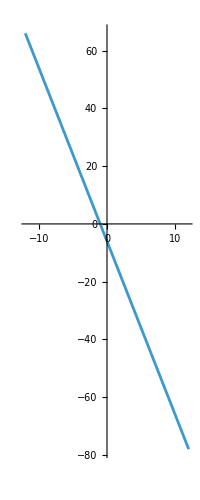

```mathematica
g1[x1_]=x2/.Solve[g1[x1,x2] == b1] [[1,1]] 
g2[x1_]=x2/.Solve[g2[x1,x2] == b2] [[1,1]] 
g3[x1_]=x2/.Solve[g3[x1,x2] == b3] [[1,1]] 
g4[x1_]=x2/.Solve[g4[x1,x2] == b4] [[1,1]] 
g5[x1_]=x2/.Solve[g5[x1,x2] == b5] [[1,1]] 

Plot[{g1[x],g2[x],g3[x],g4[x],g5[x]}, {x,-12,12}, PlotHighlighting->None, AspectRatio->Automatic]
```